## TypeII[SU(3)] + GW

```mathematica
SetDirectory["D:\\Simha\\Computation & Codes\\Mathematica"]
```

D:\Simha\Computation & Codes\Mathematica

```mathematica
Get["PDESpecialSolutionsV4-Jul4-2020.m"]
```

c::shdw: Symbol c appears in multiple contexts {Calculus`PDESpecialSolutions`,Global`}; definitions in context Calculus`PDESpecialSolutions` may shadow or be shadowed by other definitions.

i::shdw: Symbol i appears in multiple contexts {Calculus`PDESpecialSolutions`,Global`}; definitions in context Calculus`PDESpecialSolutions` may shadow or be shadowed by other definitions.

ϕ::shdw: Symbol ϕ appears in multiple contexts {Calculus`PDESpecialSolutions`,Global`}; definitions in context Calculus`PDESpecialSolutions` may shadow or be shadowed by other definitions.

n::shdw: Symbol n appears in multiple contexts {Calculus`PDESpecialSolutions`,Global`}; definitions in context Calculus`PDESpecialSolutions` may shadow or be shadowed by other definitions.

Built-in package AnalyzeAndSolveV2.m of March 13, 2010 was successfully loaded.

Package PDESpecialSolutionsV4-Jul4-2020.m from July 4, 2020 was successfully loaded on {27,12,2022}

Based on Version 4, last updated on March 30, 2020 by Robert Kragler and Willy Hereman. 
Previously updated by Hereman on September 24, 2019. 
Based on Version 3, last updated by Hereman on March 21, 2010. 
Previously updated by Goktas on December 13, 2009 and by Hereman on January 8 and January 23, 2009. 
Based on code first released by Baldwin, Goktas, and Hereman on February 28, 2005.

```mathematica
Clear[α,β,γ,m,n]
```

```mathematica
sol=PDESpecialSolutions[{D[ϕ[u],u,u]==-α ϕ[u] ψ[u]^2-3α ϕ[u] ξ[u]^2,D[ψ[u],u,u]== -α ψ[u] ϕ[u]^2-3α ξ[u]^2 ψ[u],D[ξ[u],u,u]== -α ξ[u] ϕ[u]^2-α ψ[u]^2 ξ[u]},
                                   {ϕ[u],ψ[u],ξ[u]}, {u},{α}, Verbose-> True, Form -> Cn]
```

The given system of differential equations is:

ϕ_uu==-3 α ξ^2 ϕ-α ϕ ψ^2
ψ_uu==-3 α ξ^2 ψ-α ϕ^2 ψ
ξ_uu==-α ξ ϕ^2-α ξ ψ^2

Transforming the differential equation(s) into a nonlinear ODE in CN=JacobiCN

{α u[1][CN] (u[2][CN])^2+3 α u[1][CN] (u[3][CN])^2-CN c[1]^2 u[1]'[CN]+2 CN mod c[1]^2 u[1]'[CN]-2 CN^3 mod c[1]^2 u[1]'[CN]+c[1]^2 u[1]''[CN]-CN^2 c[1]^2 u[1]''[CN]-mod c[1]^2 u[1]''[CN]+2 CN^2 mod c[1]^2 u[1]''[CN]-CN^4 mod c[1]^2 u[1]''[CN]==0,α (u[1][CN])^2 u[2][CN]+3 α u[2][CN] (u[3][CN])^2-CN c[1]^2 u[2]'[CN]+2 CN mod c[1]^2 u[2]'[CN]-2 CN^3 mod c[1]^2 u[2]'[CN]+c[1]^2 u[2]''[CN]-CN^2 c[1]^2 u[2]''[CN]-mod c[1]^2 u[2]''[CN]+2 CN^2 mod c[1]^2 u[2]''[CN]-CN^4 mod c[1]^2 u[2]''[CN]==0,α (u[1][CN])^2 u[3][CN]+α (u[2][CN])^2 u[3][CN]-CN c[1]^2 u[3]'[CN]+2 CN mod c[1]^2 u[3]'[CN]-2 CN^3 mod c[1]^2 u[3]'[CN]+c[1]^2 u[3]''[CN]-CN^2 c[1]^2 u[3]''[CN]-mod c[1]^2 u[3]''[CN]+2 CN^2 mod c[1]^2 u[3]''[CN]-CN^4 mod c[1]^2 u[3]''[CN]==0}

Time Used:0.016

Determining the maximal degree of the polynomial solutions.

The potential solutions {{m[1] -> 1, m[3] -> m[2]}, {m[2] -> 1, m[3] -> m[1]}, {m[2] -> m[1], m[3] -> 1}, {m[2] -> m[1], m[3] -> m[1]}} are being removed because they are under determined.

PDESpecialSolutions`dominantBehavior::freevalues: The solution(s) {{m[1]→1,m[2]→1},{m[1]→1,m[3]→1},{m[2]→1,m[3]→1}} 
do not fix all the values of M_i.  
We will now generate all the possible values for the free M_i up to 
the user option MaxDegreeOfThePolynomial which is set to 3 by default, 
but can be any non-negative integer.

The potential solutions {{m[1] -> 1, m[2] -> 1}, {m[1] -> 1, m[3] -> 1}, {m[1] -> 1, m[3] -> m[2]}, {m[2] -> 1, m[3] -> 1}, {m[2] -> 1, m[3] -> m[1]}, {m[2] -> m[1], m[3] -> 1}, {m[2] -> m[1], m[3] -> m[1]}} are being removed because they are (i) negative, (ii) contain freedom, (iii) fail to balance highest exponent terms from two different terms in the original system.  If M_i < 0, then the transform u -> 1/v might result in a system that PDESpecialSolutions may be able to solve.

{{m[1]→1,m[2]→1,m[3]→1}}

Time Used:0.

Seeking polynomial solutions of the form

{{u[1][CN]→a[1,0]+CN a[1,1],u[2][CN]→a[2,0]+CN a[2,1],u[3][CN]→a[3,0]+CN a[3,1]}}

Deriving the nonlinear algebraic system for the coefficients.

The nonlinear algebraic system is

{{{a[1,0] (a[2,0]^2+3 a[3,0]^2)==0,2 a[1,1] a[2,0] a[2,1]+a[1,0] a[2,1]^2+6 a[1,1] a[3,0] a[3,1]+3 a[1,0] a[3,1]^2==0,α a[2,1]^2+3 α a[3,1]^2-2 mod c[1]^2==0,α a[1,1] a[2,0]^2+2 α a[1,0] a[2,0] a[2,1]+3 α a[1,1] a[3,0]^2+6 α a[1,0] a[3,0] a[3,1]-a[1,1] c[1]^2+2 mod a[1,1] c[1]^2==0,a[2,0] (a[1,0]^2+3 a[3,0]^2)==0,a[1,1]^2 a[2,0]+2 a[1,0] a[1,1] a[2,1]+6 a[2,1] a[3,0] a[3,1]+3 a[2,0] a[3,1]^2==0,α a[1,1]^2+3 α a[3,1]^2-2 mod c[1]^2==0,2 α a[1,0] a[1,1] a[2,0]+α a[1,0]^2 a[2,1]+3 α a[2,1] a[3,0]^2+6 α a[2,0] a[3,0] a[3,1]-a[2,1] c[1]^2+2 mod a[2,1] c[1]^2==0,(a[1,0]^2+a[2,0]^2) a[3,0]==0,a[1,1]^2 a[3,0]+a[2,1]^2 a[3,0]+2 a[1,0] a[1,1] a[3,1]+2 a[2,0] a[2,1] a[3,1]==0,α a[1,1]^2+α a[2,1]^2-2 mod c[1]^2==0,2 α a[1,0] a[1,1] a[3,0]+2 α a[2,0] a[2,1] a[3,0]+α a[1,0]^2 a[3,1]+α a[2,0]^2 a[3,1]-a[3,1] c[1]^2+2 mod a[3,1] c[1]^2==0},{a[3,1],a[2,1],a[1,1],a[3,0],a[2,0],a[1,0]},{c[1]},{α,mod},{α,mod,a[1,1],a[2,1],a[3,1],c[1]}}}

Time Used:0.016

Solving the nonlinear algebraic system.

{{{a[1,0]→0,a[2,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[1,0]→0,a[2,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[1,0]→0,a[2,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[1,0]→0,a[2,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[1,0]→0,a[2,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[1,0]→0,a[2,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[1,0]→0,a[2,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[1,0]→0,a[2,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[1,0]→0,a[3,0]→0,a[2,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[1,0]→0,a[3,0]→0,a[2,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[1,0]→0,a[3,0]→0,a[2,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[1,0]→0,a[3,0]→0,a[2,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[1,0]→0,a[3,0]→0,a[2,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[1,0]→0,a[3,0]→0,a[2,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[1,0]→0,a[3,0]→0,a[2,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[1,0]→0,a[3,0]→0,a[2,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[3,0]→0,a[1,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→-(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→-c[1]/(√2 √α),a[3,1]→-c[1]/(√6 √α)},{a[2,0]→0,a[1,0]→0,a[3,0]→0,mod→1/2,a[1,1]→(√(c[1]^2))/(√2 √α),a[2,1]→c[1]/(√2 √α),a[3,1]→c[1]/(√6 √α)}}}

Time Used:0.89

Building and (numerically and/or symbolically) testing the solutions.

The possible non-trivial solutions (before any testing) are:

{{{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2}}}

Numerically testing the solutions.

The following solutions will be numerically tested:

{{{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2}}}

The following solutions passed the numerical test:

{{{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2}}}

Symbolically testing the solutions.

The following solutions will be tested symbolically:

{{{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] CN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] CN[phase+u c[1],1/2])/(√6 √α),mod→1/2}}}

The following solutions (in factored form) passed the symbolic test:

{{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2}}

The following simplification rules are being used

{Sqrt[a^2]->a}

Time Used:0.61

The final solutions were tested both numerically and symbolically.

{{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→-(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2},{ϕ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ψ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√2 √α),ξ[u]→(c[1] JacobiCN[phase+u c[1],1/2])/(√6 √α),mod→1/2}}

```mathematica
(*for a=1,2,3*)
```

```mathematica
(*ϕ(u) = ψ(u)=1/(√(2α))JacobiCN[u,1/2],ξ(u) = 1/(√(6α))JacobiCN[u,1/2]*)
(*for a=1,2,5*)
```

```mathematica
(*ϕ(u) = ψ(u)=√(2/α)JacobiCN[u,1/2],ξ(u) = (2i)/(√(3α))JacobiCN[u,1/2]*)
```

```mathematica
(*c[1]==1*)
```

```mathematica
p0=3;p3=1;k=1;l=1;m0=1;m3=3;g=0.5;α=(-g^2 k^2)/(p3^2-p0^2);β=(-g^2 l^2)/(p3^2-p0^2);γ=(-g^2(m3^2-m0^2))/(p3^2-p0^2);Ag=0.01;wg=10;
```

```mathematica
phi[z_,t_]=2/(√(5α))JacobiCN[p0 t+p3 z,1/2]
```

5.05964 JacobiCN[3 t+z,1/2]

```mathematica
psi[z_,t_]=2/(√(5β))JacobiCN[p0 t+p3 z,1/2]
```

5.05964 JacobiCN[3 t+z,1/2]

```mathematica
xi[z_,t_]=2/(√(5γ))JacobiCN[p0 t+p3 z,1/2]
```

1.78885 JacobiCN[3 t+z,1/2]

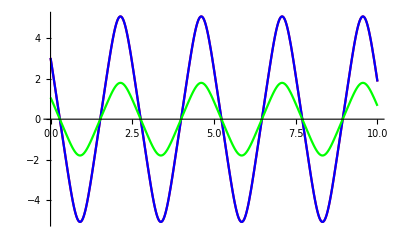

```mathematica
Plot[{phi[1,t],psi[1,t],xi[1,t]},{t,0,10},PlotStyle->{Red,Blue,Green}]
```